```mathematica
RotationsE1[alpha_]:=Module[{Re1},
Re1= {{1,0,0},{0,Cos[alpha Degree], -Sin[alpha Degree]}, {0,Sin[alpha Degree],Cos[alpha Degree]}};
Return[Re1]
];
```

```mathematica
RotationsE2[alpha_]:=Module[{Re2},
Re2 = {{Cos[alpha Degree],0,Sin[alpha Degree]},{0,1,0},{-Sin[alpha Degree],0, Cos[alpha Degree]}};
Return[Re2]
];
```

```mathematica
RotationsE3[alpha_]:=Module[{Re3},
Re3 = {{Cos[alpha Degree],-Sin[alpha Degree],0},{Sin[alpha Degree], Cos[alpha Degree],0},{0,0,1}};
Return[Re3]
];

ComputePointsFromRotatedCamera[WorldPoints_,Rotation_,Rotation2_,zeta_,e_,e2_]:=Module[{T,T2,Oc2Points,OcPoints,Tt,Tt2,ProjectionMtx,eOc,eOcNotRot,e2OcNotRot,e2Oc},

T= {{Rotation[[1,1]],Rotation[[1,2]],Rotation[[1,3]],0},{Rotation[[2,1]],Rotation[[2,2]],Rotation[[2,3]],0},{Rotation[[3,1]],Rotation[[3,2]],Rotation[[3,3]],0},{0,0,0,1}};

Tt= Transpose[T];
Print["Tt =", Tt];

T2= {{Rotation2[[1,1]],Rotation2[[1,2]],Rotation2[[1,3]],0},{Rotation2[[2,1]],Rotation2[[2,2]],Rotation2[[2,3]],0},{Rotation2[[3,1]],Rotation2[[3,2]],Rotation2[[3,3]],0},{0,0,0,1}};

Tt2 = Transpose[T2];

Oc2Points=ConstantArray[0,{4,4}];
Oc2Points[[All,1]]= Tt.WorldPoints[[All,1]];
Oc2Points[[All,2]]=Tt.WorldPoints[[All,2]];
Oc2Points[[All,3]]=Tt.WorldPoints[[All,3]];
Oc2Points[[All,4]]=Tt.WorldPoints[[All,4]];

(*Print[
"OcPoints",ListPlot[ {Oc2Points[[All,1]][[1;;2]], Oc2Points[[All,2]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,4]][[1;;2]]  }
]
];*)

Print["Oc2Points = ",MatrixForm[Oc2Points]];
Print["Oc2Points = ",MatrixForm[Rationalize[N[Oc2Points]]]];

OcPoints=ConstantArray[0,{4,4}];
OcPoints[[All,1]]= Tt2.WorldPoints[[All,1]];
OcPoints[[All,2]]=Tt2.WorldPoints[[All,2]];
OcPoints[[All,3]]=Tt2.WorldPoints[[All,3]];
OcPoints[[All,4]]=Tt2.WorldPoints[[All,4]];

Print["OcPoints = ",MatrixForm[OcPoints]];
Print["OcPoints = ",MatrixForm[Rationalize[N[OcPoints]]]];
Print[
"OcPoints = ",ListPlot[ {OcPoints[[All,1]][[1;;2]], OcPoints[[All,2]][[1;;2]],OcPoints[[All,3]][[1;;2]],OcPoints[[All,4]][[1;;2]]  }
]
];



ProjectionMtx = {{zeta,0,0,0},{0,zeta,0,0},{0,0,zeta,0},
{0,0,1,0}};

Oc2Points = ProjectionMtx.Oc2Points;

Oc2Points[[All,1]]= Oc2Points[[All,1]]/Oc2Points[[4,1]];
Oc2Points[[All,2]]= Oc2Points[[All,2]]/Oc2Points[[4,2]];
Oc2Points[[All,3]]= Oc2Points[[All,3]]/Oc2Points[[4,3]];
Oc2Points[[All,4]]= Oc2Points[[All,4]]/Oc2Points[[4,4]];
Print["Projected Oc2Points = ",MatrixForm[Rationalize[N[Oc2Points]]]];


OcPoints = ProjectionMtx.OcPoints;

OcPoints[[All,1]]= OcPoints[[All,1]]/OcPoints[[4,1]];
OcPoints[[All,2]]= OcPoints[[All,2]]/OcPoints[[4,2]];
OcPoints[[All,3]]= OcPoints[[All,3]]/OcPoints[[4,3]];
OcPoints[[All,4]]= OcPoints[[All,4]]/OcPoints[[4,4]];
Print["Projected OcPoints = ",MatrixForm[Rationalize[N[OcPoints]]]];

(*Berechnung der beiden e einmal in der ebene = e und einal außerhalb dder Ebene e2*)
eOc=Tt.e;
eOcNotRot = Tt2.e;

e2Oc = Tt.e2;
e2OcNotRot= Tt2.e2;


(*Berechnung von e in der Ebene*)
eOc=ProjectionMtx.eOc;
eOc=eOc/eOc[[4]];
eOcNotRot = ProjectionMtx.eOcNotRot;
eOcNotRot = eOcNotRot/eOcNotRot[[4]];
Print["eOc = ",MatrixForm[Rationalize[N[ eOc]]]];
Print["eOcNotRot  = ",MatrixForm[Rationalize[N[ eOcNotRot ]]]];

Print[
"Projected Oc2Points = ",Show[ListPlot[ {Oc2Points[[All,1]][[1;;2]], Oc2Points[[All,2]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,4]][[1;;2]],eOc[[1;;2]]  }],
ListLinePlot[{Oc2Points[[All,1]][[1;;2]],Oc2Points[[All,4]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,2]][[1;;2]]}]
]
];



Print[
"Projected OcPoints = ",ListPlot[ {OcPoints[[All,1]][[1;;2]], OcPoints[[All,2]][[1;;2]],OcPoints[[All,3]][[1;;2]],OcPoints[[All,4]][[1;;2]],eOcNotRot[[1;;2]]  }
]
];

(*Berechnung von e2 welches nicht in der Ebene der anderen Punkte liegt*)

e2Oc = ProjectionMtx.e2Oc;
e2Oc=e2Oc/e2Oc[[4]];

e2OcNotRot = ProjectionMtx.e2OcNotRot;
e2OcNotRot = e2OcNotRot/e2OcNotRot[[4]];
Print["e2Oc = ",MatrixForm[Rationalize[N[e2Oc]]]];
Print["e2OcNotRot = ",MatrixForm[Rationalize[N[e2OcNotRot]]]];

ComputeHomography[WorldPoints,Oc2Points,OcPoints,eOc,e2Oc,eOcNotRot,e2OcNotRot ];

];

ComputeHomography[WorldPoints_,Oc2Points_,OcPoints_,eOc_,e2Oc_,eOcNotRot_,e2OcNotRot_]:=Module[{H,Oc2TestPointsH,eOcTestPointsH,e2OcTestPointsH,CoefficientMtx,nullspace,Oc2PointsOfHomography,eOcPointsOfHomography,e2OcPointsOfHomography},

CoefficientMtx= ConstantArray[0,{8,9}];
CoefficientMtx[[1]]=
{OcPoints[[1,1]],OcPoints[[2,1]],1,0,0,0,-OcPoints[[1,1]]*Oc2Points[[1,1]],-OcPoints[[2,1]]*Oc2Points[[1,1]],-Oc2Points[[1,1]]};
CoefficientMtx[[2]]=
{0,0,0,OcPoints[[1,1]],OcPoints[[2,1]],1,-OcPoints[[1,1]]*Oc2Points[[2,1]],-OcPoints[[2,1]]*Oc2Points[[2,1]],-Oc2Points[[2,1]]};
CoefficientMtx[[3]]=
{OcPoints[[1,2]],OcPoints[[2,2]],1,0,0,0,-OcPoints[[1,2]]*Oc2Points[[1,2]],-OcPoints[[2,2]]*Oc2Points[[1,2]],-Oc2Points[[1,2]]};
CoefficientMtx[[4]]=
{0,0,0,OcPoints[[1,2]],OcPoints[[2,2]],1,-OcPoints[[1,2]]*Oc2Points[[2,2]],-OcPoints[[2,2]]*Oc2Points[[2,2]],-Oc2Points[[2,2]]};
CoefficientMtx[[5]]=
{OcPoints[[1,3]],OcPoints[[2,3]],1,0,0,0,-OcPoints[[1,3]]*Oc2Points[[1,3]],-OcPoints[[2,3]]*Oc2Points[[1,3]],-Oc2Points[[1,3]]};
CoefficientMtx[[6]]=
{0,0,0,OcPoints[[1,3]],OcPoints[[2,3]],1,-OcPoints[[1,3]]*Oc2Points[[2,3]],-OcPoints[[2,3]]*Oc2Points[[2,3]],-Oc2Points[[2,3]]};
CoefficientMtx[[7]]=
{OcPoints[[1,4]],OcPoints[[2,4]],1,0,0,0,-OcPoints[[1,4]]*Oc2Points[[1,4]],-OcPoints[[2,4]]*Oc2Points[[1,4]],-Oc2Points[[1,4]]};
CoefficientMtx[[8]]=
{0,0,0,OcPoints[[1,4]],OcPoints[[2,4]],1,-OcPoints[[1,4]]*Oc2Points[[2,4]],-OcPoints[[2,4]]*Oc2Points[[2,4]],-Oc2Points[[2,4]]};

(*Print["CoefficientMtx = ", MatrixForm[CoefficientMtx]]*)Print["CoefficientMtx = ", MatrixForm[Rationalize[N[CoefficientMtx]]]];

nullspace = NullSpace[CoefficientMtx];
Print["NullSpace = ",MatrixForm[nullspace] ];

H={{nullspace[[1,1]],nullspace[[1,2]],nullspace[[1,3]]},{nullspace[[1,4]],nullspace[[1,5]],nullspace[[1,6]]},{nullspace[[1,7]],nullspace[[1,8]],nullspace[[1,9]]}};
Print["H = ",MatrixForm[Rationalize[N [H]]]];

Oc2TestPointsH = {{OcPoints[[1,1]],OcPoints[[1,2]],OcPoints[[1,3]],OcPoints[[1,4]]},{OcPoints[[2,1]],OcPoints[[2,2]],OcPoints[[2,3]],OcPoints[[2,4]]},
{1,1,1,1}};

Print["TestPoints = ", MatrixForm[Oc2TestPointsH]];

Oc2PointsOfHomography = H.Oc2TestPointsH;

Print["Oc2PointsOfHomography = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography]]]];



If[Oc2PointsOfHomography[[3,1]]≠0, Print["Oc2PointsOfHomography A = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,1]]/Oc2PointsOfHomography[[3,1]]]]]],Print["Oc2PointsOfHomography A = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,1]]]]]]];

If[Oc2PointsOfHomography[[3,2]]≠0, Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,2]]/Oc2PointsOfHomography[[3,2]]]]]],Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,2]]]]]]];

If[Oc2PointsOfHomography[[3,3]]≠0, Print["Oc2PointsOfHomography C = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,3]]/Oc2PointsOfHomography[[3,3]]]]]],Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,3]]]]]]];

If[Oc2PointsOfHomography[[3,4]]≠0, Print["Oc2PointsOfHomography D = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,4]]/Oc2PointsOfHomography[[3,4]]]]]],Print["Oc2PointsOfHomography D = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,4]]]]]]];



(*Berechnung des Punktes e in der Ebene mit der gleichen H wie die 4 restlichen Punkte*)
eOcTestPointsH = {eOcNotRot [[1]],eOcNotRot [[2]],1};
eOcPointsOfHomography = H.eOcTestPointsH;
Print["eOcPointsOfHomography = ", MatrixForm[Rationalize[N[eOcPointsOfHomography ]]]];
If[eOcPointsOfHomography[[3]]≠0, Print["eOcPointsOfHomography E = ",MatrixForm[Rationalize[N[eOcPointsOfHomography/eOcPointsOfHomography[[3]]]]]],Print["eOcPointsOfHomography E = ",MatrixForm[Rationalize[N[eOcPointsOfHomography]]]]];

(*Berechnung des Punktes e welcher nicht in der Ebene liegt mit der gleichen H wie die 4 restlichen Punkte und e in der Ebene*)
e2OcTestPointsH = {e2OcNotRot[[1]],e2OcNotRot[[2]],1};
e2OcPointsOfHomography = H.e2OcTestPointsH;
Print["e2OcPointsOfHomography = ", MatrixForm[Rationalize[N[e2OcPointsOfHomography ]]]];
If[e2OcPointsOfHomography[[3]]≠0, Print["e2OcPointsOfHomography E2 = ",MatrixForm[Rationalize[N[e2OcPointsOfHomography/e2OcPointsOfHomography[[3]]]]]],Print["eOcPointsOfHomography E2 = ",MatrixForm[Rationalize[N[e2OcPointsOfHomography]]]]];

];
```

```mathematica
alpha=45;
```

```mathematica
a={3,3,-2,1};
```

```mathematica
b={5,3,-2,1};
```

```mathematica
c={3,5,-2,1};
```

```mathematica
d={5,5,-2,1};
```

```mathematica
e={4,4,-2,1};
```

```mathematica
e2={4,4,-6,1};
```

```mathematica
Oc={0,0,0,1};
```

```mathematica
zeta= -1;
```

```mathematica
WorldPoints={{a[[1]],b[[1]],c[[1]],d[[1]]},{a[[2]],b[[2]],c[[2]],d[[2]]},{a[[3]],b[[3]],c[[3]],d[[3]]},{a[[4]],b[[4]],c[[4]],d[[4]]}};
```

Tt ={{1/(√2),0,-1/(√2),0},{0,1,0,0},{1/(√2),0,1/(√2),0},{0,0,0,1}}

Oc2Points = (3/(√2)+√2 | 5/(√2)+√2 | 3/(√2)+√2 | 5/(√2)+√2
3 | 3 | 5 | 5
3/(√2)-√2 | 5/(√2)-√2 | 3/(√2)-√2 | 5/(√2)-√2
1 | 1 | 1 | 1)

Oc2Points = (3.53553 | 4.94975 | 3.53553 | 4.94975
3 | 3 | 5 | 5
0.707107 | 2.12132 | 0.707107 | 2.12132
1 | 1 | 1 | 1)

OcPoints = (3 | 5 | 3 | 5
3 | 3 | 5 | 5
-2 | -2 | -2 | -2
1 | 1 | 1 | 1)

OcPoints = (3 | 5 | 3 | 5
3 | 3 | 5 | 5
-2 | -2 | -2 | -2
1 | 1 | 1 | 1)

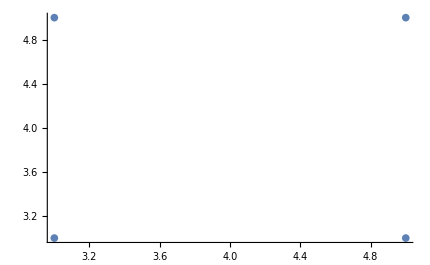
OcPoints = -Graphics-

Projected Oc2Points = (-5 | -7/3 | -5 | -7/3
-4.24264 | -1.41421 | -7.07107 | -2.35702
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

Projected OcPoints = (3/2 | 5/2 | 3/2 | 5/2
3/2 | 3/2 | 5/2 | 5/2
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

eOc = (-3
-2.82843
-1
1)

eOcNotRot  = (2
2
-1
1)

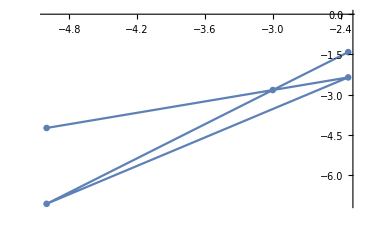
Projected Oc2Points = -Graphics-

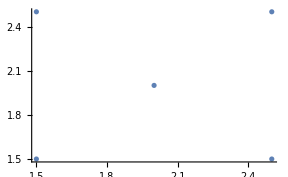
Projected OcPoints = -Graphics-

e2Oc = (5
2.82843
-1
1)

e2OcNotRot = (2/3
2/3
-1
1)

CoefficientMtx = (3/2 | 3/2 | 1 | 0 | 0 | 0 | 15/2 | 15/2 | 5
0 | 0 | 0 | 3/2 | 3/2 | 1 | 6.36396 | 6.36396 | 4.24264
5/2 | 3/2 | 1 | 0 | 0 | 0 | 35/6 | 7/2 | 7/3
0 | 0 | 0 | 5/2 | 3/2 | 1 | 3.53553 | 2.12132 | 1.41421
3/2 | 5/2 | 1 | 0 | 0 | 0 | 15/2 | 25/2 | 5
0 | 0 | 0 | 3/2 | 5/2 | 1 | 10.6066 | 17.6777 | 7.07107
5/2 | 5/2 | 1 | 0 | 0 | 0 | 35/6 | 35/6 | 7/3
0 | 0 | 0 | 5/2 | 5/2 | 1 | 5.89256 | 5.89256 | 2.35702)

NullSpace = (1 | 0 | 1 | 0 | √2 | 0 | -1 | 0 | 1)

H = (1 | 0 | 1
0 | 1.41421 | 0
-1 | 0 | 1)

TestPoints = (3/2 | 5/2 | 3/2 | 5/2
3/2 | 3/2 | 5/2 | 5/2
1 | 1 | 1 | 1)

Oc2PointsOfHomography = (5/2 | 7/2 | 5/2 | 7/2
2.12132 | 2.12132 | 3.53553 | 3.53553
-1/2 | -3/2 | -1/2 | -3/2)

Oc2PointsOfHomography A = (-5
-4.24264
1)

Oc2PointsOfHomography B = (-7/3
-1.41421
1)

Oc2PointsOfHomography C = (-5
-7.07107
1)

Oc2PointsOfHomography D = (-7/3
-2.35702
1)

eOcPointsOfHomography = (3
2.82843
-1)

eOcPointsOfHomography E = (-3
-2.82843
1)

e2OcPointsOfHomography = (5/3
0.942809
1/3)

e2OcPointsOfHomography E2 = (5
2.82843
1)

```mathematica
ComputePointsFromRotatedCamera[WorldPoints,RotationsE2[45],RotationsE2[0],zeta,e,e2];
```